```mathematica
CloseStreams[];ArrayPlot[
Table[
Table[{p,RatioFor[tuple,{p}]}, {p, tuple}]
,{tuple, Subsets[Prime[Range[2,25]],{2}]}
]
,
PlotRange->All,
GridLines->{Automatic,Append[Table[t,{t,0,1,0.1}],{0.45,{Red,Thick}}]},
Frame->True,
ImageSize->1000
]
```

```mathematica
Needs["Polytopes`"]
```

Needs[Polytopes`]

```mathematica
Needs["Polytopes`"]
```

```mathematica
CloseStreams[];
ListLinePlot[
Table[
Table[{p,Det[MatrixForm[{{q,RatioFor[Sort[{q,p}],{q}]},{RatioFor[Sort[{q,p}],{p}],p }}]]},
{p, Select[Prime[Range[2,10]],# ≠ q&]}
]
,{q,Prime[Range[2,10]]}
],
PlotMarkers->None,
PlotLabel->"Determinant of {{p,Ratio[{p,q},p}],{Ratio[{p,q},q},q]] versus p"
]
```

-Graphics-

```mathematica
Solve[Det[{{p,a},{b,q}}]==v, a]
```

{{a→(p q-v)/b}}

```mathematica
PrimePi[139]
```

34

```mathematica
Area[{{61,0.908485},{3,0.645355},{183,0.5632159999999999}}]
```

```mathematica
Area[{{61,0.908485},{3,0.645355},{183,0.5632159999999999}}]
```

Area[{{61,0.908485},{3,0.645355},{183,0.563216}}]

```mathematica
d= Polygon[{61,0.908485},{3,0.645355},{183,0.5632159999999999}]
```

Polygon[{61,0.908485},{3,0.645355},{183,0.563216}]

```mathematica
Area[d]
```

Area[Polygon[{61,0.908485},{3,0.645355},{183,0.563216}]]

```mathematica
MatrixForm[{{q,RatioFor[Sort[{q,p}],{q}]},{RatioFor[Sort[{q,p}],{p}],p }}]
```

$Aborted

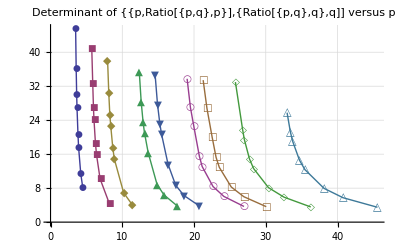

```mathematica
CloseStreams[];
With[
{max=10},
ListLinePlot[
Table[
Table[{q / RatioFor[Sort[{q,p}],{p}]   ,p / RatioFor[Sort[{q,p}],{q}]},
{p, Select[Prime[Range[2,max]],# ≠ q&]}
]
,{q,Prime[Range[2,max]]}
]
,
GridLines->Automatic,
PlotMarkers->Automatic,
PlotLabel->"Determinant of {{p,Ratio[{p,q},p}],{Ratio[{p,q},q},q]] versus p"
]
]
```

```mathematica
With[
{max=3},
Table[
Table[{p,Det[MatrixForm[{{RatioFor[Sort[{q,p}],{q}],RatioFor[Sort[{q,p}],{p,q}]},{RatioFor[Sort[{q,p}],{p,q}],RatioFor[Sort[{q,p}],{p}] }}]]},
{p, Select[Prime[Range[2,max]],# ≠ q&]}
]
,{q,Prime[Range[2,max]]}
]
]
```

{{{5,Det[(0.611916 | 0.335896
0.335896 | 0.667874)]}},{{3,Det[(0.667874 | 0.335896
0.335896 | 0.611916)]}}}

```mathematica
N[Det[({{0.611916, 0.335896}, {0.335896, 0.667874}})]]
```

0.295857

```mathematica
Det[({{a, b}, {c, d}})]
```

-b c+a d